# Leading order

## Load FeynCalc

```mathematica
description="Leading order cross section of slepton pair production.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
FCCheckVersion[9,3,1];
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Calculate the squared amplitude

### Draw diagrams

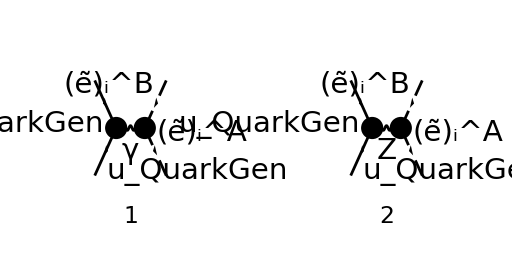

```mathematica
diags=InsertFields[
CreateTopologies[0,2->2],{F[3,{QuarkGen}],-F[3,{QuarkGen}]}->{-S[12,{B,i}],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{S[1],S[2],S[3],S[4]}
];
Paint[
diags,
ColumnsXRows->{2,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,256}
];
```

### Make output prettier

```mathematica
MakeBoxes[p1, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(1\)]\)";
MakeBoxes[p2, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(2\)]\)";
MakeBoxes[p3, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(3\)]\)"; 
MakeBoxes[p4, TraditionalForm] := "\!\(\*SubscriptBox[\(p\),\(4\)]\)";
```

### Compute amplitude

```mathematica
M[0]=FCFAConvert[
CreateFeynAmp[diags],(*Create amplitudes in FeynArts*)
IncomingMomenta->{p1,p2},(*Define incoming momenta*)
OutgoingMomenta->{p3,p4},(*Define outgoing momenta*)
ChangeDimension->4,(*Define spacetime dimension*)
UndoChiralSplittings->True,(*No left/right-splitting in Mγ*)
List->False,(*Output the amplitude alone, not in a list*)
Contract->True,(*Replace  with *)
DropSumOver->True,(*SumOver from FeynArts is dropped. Einstein summation applies, so it is not needed.*)
SMP->True (*Use SMP for parameters (e.g. SMP["m_e"] = electron mass)*)
(*Prefactor->3/2 SMP["e_Q"](*General quark charge, not just up*) NOTE TO SELF: This changes the prefactor for both diagrams, which is not what we want! There is no quark charge in the Z-diagram.*)
]/.{MQU[QuarkGen]->0}
```

(2 e^2 δ_Col1Col2 IndexDelta(A,B) (φ(-OverBar[p_2])).(γ̄·(OverBar[p_3]-OverBar[p_4])).(φ(OverBar[p_1])))/(3 (OverBar[p_3]+OverBar[p_4])^2)-(ⅈ e (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-OverBar[p_2])).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ̄·(OverBar[p_3]-OverBar[p_4])).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ̄·(OverBar[p_3]-OverBar[p_4])).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])))/(2 (cos(θ_W)) (sin(θ_W)) ((OverBar[p_3]+OverBar[p_4])^2-m_Z^2))

Change  to for quark charge in photon diagram.

```mathematica
Mγ[0]=Part[M[0],1] 3/2 SMP["e_Q"];
MZ[0]=Part[M[0],2];
M[1]=Mγ[0]+MZ[0]
```

(e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-OverBar[p_2])).(γ̄·(OverBar[p_3]-OverBar[p_4])).(φ(OverBar[p_1])))/(OverBar[p_3]+OverBar[p_4])^2-(ⅈ e (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-OverBar[p_2])).((2 ⅈ e δ_Col1Col2 (sin(θ_W)) (γ̄·(OverBar[p_3]-OverBar[p_4])).(γ̄)^6)/(3 (cos(θ_W)))+(ⅈ e δ_Col1Col2 (4 (sin(θ_W))^2-3) (γ̄·(OverBar[p_3]-OverBar[p_4])).(γ̄)^7)/(6 (cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])))/(2 (cos(θ_W)) (sin(θ_W)) ((OverBar[p_3]+OverBar[p_4])^2-m_Z^2))

Rewrite the “chiral coefficients” into and .

```mathematica
M[2]=M[1]/.{4 SMP["sin_W"]^2-3:>12 Zql};
M[3]=M[2]/.{SMP["sin_W"]/SMP["cos_W"]:>3 Zqr / (SMP["sin_W"] SMP["cos_W"])}
```

(e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-OverBar[p_2])).(γ̄·(OverBar[p_3]-OverBar[p_4])).(φ(OverBar[p_1])))/(OverBar[p_3]+OverBar[p_4])^2-(ⅈ e (2 (sin(θ_W))^2 USf(2,i)(A,2) Conjugate[(USf(2,i)(B,2))]+(2 (sin(θ_W))^2-1) USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-OverBar[p_2])).((2 ⅈ e Zql δ_Col1Col2 (γ̄·(OverBar[p_3]-OverBar[p_4])).(γ̄)^7)/((cos(θ_W)) (sin(θ_W)))+(2 ⅈ e Zqr δ_Col1Col2 (γ̄·(OverBar[p_3]-OverBar[p_4])).(γ̄)^6)/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_1])))/(2 (cos(θ_W)) (sin(θ_W)) ((OverBar[p_3]+OverBar[p_4])^2-m_Z^2))

Rewrite the sfermion mixing matrices USf into .

```mathematica
M[4]=M[3]//.{USf[2,i][A,2] Conjugate[USf[2,i][B,2]]:>KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]}//Simplify
```

(e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-OverBar[p_2])).(γ̄·(OverBar[p_3]-OverBar[p_4])).(φ(OverBar[p_1])))/(OverBar[p_3]+OverBar[p_4])^2-(ⅈ e (2 (sin(θ_W))^2 A,B-USf(2,i)(A,1) Conjugate[(USf(2,i)(B,1))]) (φ(-OverBar[p_2])).(2 ⅈ e δ_Col1Col2 (Zql (γ̄·(OverBar[p_3]-OverBar[p_4])).(γ̄)^7+Zqr (γ̄·(OverBar[p_3]-OverBar[p_4])).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(OverBar[p_1])))/(2 (cos(θ_W)) (sin(θ_W)) ((OverBar[p_3]+OverBar[p_4])^2-m_Z^2))

```mathematica
M[5]=M[4]//.{2SMP["sin_W"]^2 KroneckerDelta[A,B]-USf[2,i][A,1] Conjugate[USf[2,i][B,1]]->-2 ZliAB}
```

(e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(-OverBar[p_2])).(γ̄·(OverBar[p_3]-OverBar[p_4])).(φ(OverBar[p_1])))/(OverBar[p_3]+OverBar[p_4])^2+(ⅈ e ZliAB (φ(-OverBar[p_2])).(2 ⅈ e δ_Col1Col2 (Zql (γ̄·(OverBar[p_3]-OverBar[p_4])).(γ̄)^7+Zqr (γ̄·(OverBar[p_3]-OverBar[p_4])).(γ̄)^6))/((cos(θ_W)) (sin(θ_W))).(φ(OverBar[p_1])))/((cos(θ_W)) (sin(θ_W)) ((OverBar[p_3]+OverBar[p_4])^2-m_Z^2))

Find the complex conjugate of the amplitude.

```mathematica
MCC[5]=ComplexConjugate[M[5]]
```

(e^2 e_Q δ_Col1Col2 IndexDelta(A,B) (φ(OverBar[p_1])).(γ̄·(OverBar[p_3]-OverBar[p_4])).(φ(-OverBar[p_2])))/(OverBar[p_3]+OverBar[p_4])^2-(2 e^2 ZliAB δ_Col1Col2 (φ(OverBar[p_1])).(Zql (γ̄)^6.(γ̄·(OverBar[p_3]-OverBar[p_4]))+Zqr (γ̄)^7.(γ̄·(OverBar[p_3]-OverBar[p_4]))).(φ(-OverBar[p_2])))/((cos(θ_W))^2 (sin(θ_W))^2 ((OverBar[p_3]+OverBar[p_4])^2-m_Z^2))

### Square the amplitudes

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-p3,-p4,0,0,MSf[B,2,i],MSf[A,2,i]];
```

```mathematica
MSquared[0]=(M[5] MCC[5])//FeynAmpDenominatorExplicit//FermionSpinSum[#,ExtraFactor->1/(4 SUNN^2)]&//DiracSimplify//SUNSimplify[#,SUNNToCACF->False]&//TrickMandelstam[#,{s,t,u,MSf[B,2,i]^2+MSf[A,2,i]^2}]&//Simplify
```

(2 e^4 (t u-(MSf(A,2,i))^2 (MSf(B,2,i))^2) (2 s^2 ZliAB^2 (Zql^2+Zqr^2)-e_Q (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2 IndexDelta(A,B) (e_Q (cos(θ_W))^2 (m_Z^2-s) (sin(θ_W))^2+2 s ZliAB (Zql+Zqr))))/(N s^2 (cos(θ_W))^4 (s-m_Z^2)^2 (sin(θ_W))^4)

### Compare with hand calculation

```mathematica
gammaZ=0;
FqliAB=SMP["e_Q"]^2 IndexDelta[A,B]-SMP["e_Q"]ZliAB IndexDelta[A,B] s (s-SMP["m_Z"]^2)/(SMP["sin_W"]^2 SMP["cos_W"]^2 ((s-SMP["m_Z"]^2)^2+SMP["m_Z"]^2 gammaZ^2)) 2(Zql+Zqr)+(ZliAB)^2 s^2 2(Zql^2+Zqr^2)/(((s-SMP["m_Z"]^2)^2+SMP["m_Z"]^2 gammaZ^2) SMP["sin_W"]^4 SMP["cos_W"]^4)
```

-(2 s ZliAB e_Q (Zql+Zqr) IndexDelta(A,B))/((cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2)+e_Q^2 IndexDelta(A,B)+(2 s^2 ZliAB^2 (Zql^2+Zqr^2))/((cos(θ_W))^4 (s-m_Z^2)^2 (sin(θ_W))^4)

```mathematica
handCalc=SMP["e"]^4/(4 SUNN s^2) FqliAB DiracTrace[GS[p2,p3-p4,p1,p3-p4],DiracTraceEvaluate->True]//DiracSimplify//TrickMandelstam[#,{s,t,u,MSf[B,2,i]^2+MSf[A,2,i]^2}]&//Simplify
```

(2 e^4 (t u-(MSf(A,2,i))^2 (MSf(B,2,i))^2) (2 s^2 ZliAB^2 (Zql^2+Zqr^2)-e_Q (cos(θ_W))^2 (s-m_Z^2) (sin(θ_W))^2 IndexDelta(A,B) (e_Q (cos(θ_W))^2 (m_Z^2-s) (sin(θ_W))^2+2 s ZliAB (Zql+Zqr))))/(N s^2 (cos(θ_W))^4 (s-m_Z^2)^2 (sin(θ_W))^4)

```mathematica
FCCompareResults[{MSquared[0]},{handCalc},Text->{"Compare to hand calculation:", "CORRECT!","WRONG!"},Interrupt->{Hold[Quit[1]],Automatic}];
```

Compare to hand calculation: CORRECT!